Project1,Lindstedt method - Damping case
Pietro De Checchi, Gaia Marangon

__________________
Equations of motion
================

```mathematica
nmax=2;
difx=v
difv=-ω0^2(1+mbk*ε*Cos[u2])(x)-2 *mbk*b*v//Expand (*SIMPLIFIED Sin Expansion*)
(*difv=-ω0^2(1+mbk*ε*Cos[u2])(x-mbk*x^3/6)-2 *mbk*b*v//Expand*)
```

v

-2 b mbk v-x ω0^2-mbk x ε ω0^2 Cos[u2]

____________________________________________________________________
Move to q,p variables (eigenvectors of the linearized equations of motion)
============================================================

```mathematica
xvsolveqp={x->(q+p)/Sqrt[ω0],v->I*Sqrt[ω0]*(q-p)}
qpsolvexv=Solve[{x==(q+p)/Sqrt[ω0],v==I*Sqrt[ω0]*(q-p)},{q,p}][[1]]//Expand//Simplify
difq=(q/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp
difp=(p/.qpsolvexv/.{x->difx,v->difv}//Expand)/.xvsolveqp//Expand//TrigToExp
```

{x→(p+q)/(√ω0),v→ⅈ (-p+q) √ω0}

{q→(-ⅈ v+x ω0)/(2 √ω0),p→(ⅈ v+x ω0)/(2 √ω0)}

b mbk p-b mbk q+ⅈ q ω0+1/4 ⅈ ⅇ^(-ⅈ u2) mbk p ε ω0+1/4 ⅈ ⅇ^(ⅈ u2) mbk p ε ω0+1/4 ⅈ ⅇ^(-ⅈ u2) mbk q ε ω0+1/4 ⅈ ⅇ^(ⅈ u2) mbk q ε ω0

-b mbk p+b mbk q-ⅈ p ω0-1/4 ⅈ ⅇ^(-ⅈ u2) mbk p ε ω0-1/4 ⅈ ⅇ^(ⅈ u2) mbk p ε ω0-1/4 ⅈ ⅇ^(-ⅈ u2) mbk q ε ω0-1/4 ⅈ ⅇ^(ⅈ u2) mbk q ε ω0

____________________________________________________________________
Expansion of the equations of motion
============================================================

```mathematica
repser={q->Sum[mbk^k*q[k],{k,0,nmax}],p->Sum[mbk^k*p[k],{k,0,nmax}]};
difqser=difq/.repser//Expand;
difpser=difp/.repser//Expand;
qdotser=(Sum[Sum[mbk^k ωr[k],{k,0,nmax-l}]*(mbk^l*dqur[l]),{l,0,nmax}]+
Sum[Sum[mbk^k ωi[k],{k,0,nmax-l}]*(mbk^l*dqui[l]),{l,0,nmax}]+
ω*Sum[mbk^k*dqu2[k],{k,0,nmax}]//Expand)/.{ωr[0]->ω0,ωi[0]->0};
pdotser=(Sum[Sum[mbk^k ωr[k],{k,0,nmax-l}]*(mbk^l*dpur[l]),{l,0,nmax}]+
Sum[Sum[mbk^k ωi[k],{k,0,nmax-l}]*(mbk^l*dpui[l]),{l,0,nmax}]+
ω*Sum[mbk^k*dpu2[k],{k,0,nmax}]//Expand)/.{ωr[0]->ω0,ωi[0]->0};
eqqser=difqser-qdotser;
eqpser=difpser-pdotser;
```

```mathematica
Coefficient[eqqser,mbk,0]
Coefficient[eqpser,mbk,0]
```

-ω dqu2[0]-ω0 dqur[0]+ⅈ ω0 q[0]

-ω dpu2[0]-ω0 dpur[0]-ⅈ ω0 p[0]

```mathematica
Coefficient[eqqser,mbk,1]
```

-ω dqu2[1]-ω0 dqur[1]+b p[0]+1/4 ⅈ ⅇ^(-ⅈ u2) ε ω0 p[0]+1/4 ⅈ ⅇ^(ⅈ u2) ε ω0 p[0]-b q[0]+1/4 ⅈ ⅇ^(-ⅈ u2) ε ω0 q[0]+1/4 ⅈ ⅇ^(ⅈ u2) ε ω0 q[0]+ⅈ ω0 q[1]-dqui[0] ωi[1]-dqur[0] ωr[1]

____________________________________________________________________
Solution at order 0 
============================================================

```mathematica
solqporder[0]={q[0]->C1*E^(I*ur-ui),p[0]->C2*E^(-I*ur-ui)};
(*Distinguish real and imaginary part in Ω and u*)
(*With this setting the secular parts for q and p will give the same corrections ωi[1],ωr[1])*)
qsol[0]=q[0]/.solqporder[0];
psol[0]=p[0]/.solqporder[0];
solqpallorder[0]=Flatten[{solqporder[0],dqur[0]->D[qsol[0],ur],dqui[0]->D[qsol[0],ui],dqu2[0]->D[qsol[0],u2],dpur[0]->D[psol[0],ur],dpui[0]->D[psol[0],ui],dpu2[0]->D[psol[0],u2]}]
```

{q[0]→C1 ⅇ^(-ui+ⅈ ur),p[0]→C2 ⅇ^(-ui-ⅈ ur),dqur[0]→ⅈ C1 ⅇ^(-ui+ⅈ ur),dqui[0]→-C1 ⅇ^(-ui+ⅈ ur),dqu2[0]→0,dpur[0]→-ⅈ C2 ⅇ^(-ui-ⅈ ur),dpui[0]→-C2 ⅇ^(-ui-ⅈ ur),dpu2[0]→0}

____________________________________________________________________
Iterative computation of the Lindstedt series at orders 1 to nmax
============================================================

```mathematica
Do[
Print["order ",iord," computing"];
Clear[eqqorder,eqporder,lisexpq,lisexpp,eqqordernew,eqpordernew,eqqordernonsec,eqpordernonsec];
eqqorder=(Coefficient[eqqser,mbk,iord]/.Flatten[Table[solqpallorder[j],{j,0,iord-1}]])/.{q[iord]->0,dqur[iord]->0,dqui[iord]->0,dqu2[iord]->0}//Expand;
eqporder=(Coefficient[eqpser,mbk,iord]/.Flatten[Table[solqpallorder[j],{j,0,iord-1}]])/.{p[iord]->0,dpur[iord]->0,dpui[iord]->0,dpu2[iord]->0}//Expand;
(*      Print[eqqorder];        *)
lisexpq=Union[Table[E^(Exponent[eqqorder[[i]],E]//Expand),{i,1,Length[eqqorder]}]] ;
lisexpp=Union[Table[E^(Exponent[eqporder[[i]],E]//Expand),{i,1,Length[eqporder]}]];
eqqordernew=Sum[((Coefficient[eqqorder,lisexpq[[i]]]/.{E^w_->0})//Simplify)*lisexpq[[i]],{i,1,Length[lisexpq]}] ;
eqpordernew=Sum[((Coefficient[eqporder,lisexpp[[i]]]/.{E^w_->0})//Simplify)*lisexpp[[i]],{i,1,Length[lisexpp]}];
(*           Print[eqqordernew];   *)

(*ISOLATE SECULAR TERM AND SOLVE FOR ωr[iord],ωi[iord]*)
(*Secolari hanno: mr=1,mi=qualunque, m2=0*)
(*secularTempq: pezzi con mr=1; li scorro uno a uno e: 
- Exponent[secularTempq[[count]],E]: esponente di singolo pezzo;
  - Coefficient[Exponent[secularTempq[[count]],E],u2] = m2 
 --> se lui è zero, allora termine sarà in secolare: Boole[...] vale 1 se secolare, 0 altrimenti
 --> se secolare, pezzo in analisi viene sommato, e conteggiato tra i secolari (altrim sommo 0) *)
secularTempq = Coefficient[eqqordernew,E^(I*ur)] ;
secularq = Sum[ secularTempq[[count]] *  Boole[Coefficient[Exponent[secularTempq[[count]],E],u2]==0],{count,1,Length[secularTempq]}]//Evaluate;
(*Isolate real and imaginary part of secular term, set both to zero to get ωr[iord] and ωi[iord]*)
secularq re = Simplify[Re[secularq],Assumptions->Flatten[{b ∈ Reals,C1 ∈ Reals,C2 ∈ Reals, ω0∈ Reals,ωr[iord]∈ Reals,ωi[iord]∈ Reals,ui∈ Reals, ε∈ Reals, ω∈ Reals,b!=0,C1!=0,C2!=0,ω0>0,Table[ω^2 !=n^2 * ω0^2, {n,1,nmax}] }]];
secularq im = Simplify[Im[secularq],Assumptions->Flatten[{b ∈ Reals,C1 ∈ Reals,C2 ∈ Reals, ω0∈ Reals,ωr[iord]∈ Reals,ωi[iord]∈ Reals,ui∈ Reals, ε∈ Reals, ω∈ Reals,b!=0,C1!=0,C2!=0,ω0>0 ,Table[ω^2 !=n^2 * ω0^2, {n,1,nmax}]}]];
solome[iord ]=Solve[{secularq re==0,secularq im==0},{ωr[iord],ωi[iord]}][[1]]  //Simplify//Expand;

(*GO BACK TO iord-EQUA, ELIMINATE SECULAR*)
eqqordernonsec=eqqordernew /.solome[iord] //Expand;
eqpordernonsec=eqpordernew/.solome[iord] //Expand;

(*GET q,p SOLUTIONS*)
qsol[iord]=Sum[(eqqordernonsec[[i]]/((Exponent[eqqordernonsec[[i]],E]/.{ur->ω0,ui->0,u2->ω})-I*ω0))/.{E^w_->E^ExpandAll[w]},{i,1,Length[eqqordernonsec]}]//ExpToTrig//Simplify//TrigToExp//Expand;
psol[iord]=Sum[eqpordernonsec[[i]]/((Exponent[eqpordernonsec[[i]],E]/.{ur->ω0,ui->0,u2->ω})+I*ω0)/.{E^w_->E^ExpandAll[w]},{i,1,Length[eqpordernonsec]}]//ExpToTrig//Simplify//TrigToExp//Expand;
solqpallorder[iord]=Flatten[{q[iord]->qsol[iord],p[iord]->psol[iord],dqur[iord]->D[qsol[iord],ur],dqui[iord]->D[qsol[iord],ui],dqu2[iord]->D[qsol[iord],u2],dpur[iord]->D[psol[iord],ur],dpui[iord]->D[psol[iord],ui],dpu2[iord]->D[psol[iord],u2],solome[iord]}];

Print["order ",iord," computed"],
{iord,1,nmax}];
```

order 1 computing

order 1 computed

order 2 computing

order 2 computed

```mathematica
solqpallorder[0]
solqpallorder[1]
solqpallorder[2]
```

{q[0]→C1 ⅇ^(-ui+ⅈ ur),p[0]→C2 ⅇ^(-ui-ⅈ ur),dqur[0]→ⅈ C1 ⅇ^(-ui+ⅈ ur),dqui[0]→-C1 ⅇ^(-ui+ⅈ ur),dqu2[0]→0,dpur[0]→-ⅈ C2 ⅇ^(-ui-ⅈ ur),dpui[0]→-C2 ⅇ^(-ui-ⅈ ur),dpu2[0]→0}

{q[1]→(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),p[1]→-(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))+(2 ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dqur[1]→(b C2 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 b C2 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dqui[1]→-(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))+(2 ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dqu2[1]→(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dpur[1]→(b C1 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 b C1 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)-(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dpui[1]→(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),dpu2[1]→-(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(ⅈ C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(ⅈ C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2)),ωr[1]→0,ωi[1]→b}

{q[2]→-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),p[2]→(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dqur[2]→-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-ui-ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dqui[2]→(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dqu2[2]→-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dpur[2]→(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-ui+ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dpui[2]→-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),dpu2[2]→(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4)),ωr[2]→-b^2/(2 ω0)+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)),ωi[2]→0}

```mathematica
ω0

ωr[1]/.solqpallorder[1]
ωi[1]/.solqpallorder[1]

ωr[2]/.solqpallorder[2]
ωi[2]/.solqpallorder[2]
```

ω0

0

b

-b^2/(2 ω0)+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2))

0

____________________________________________________________________
Compose complete solutions, taking care of initial conditions
============================================================

```mathematica
Do[
completeqSol[ordSol] = (q[0]/.solqpallorder[0])+Sum[(q[iord]/.solqpallorder[iord])- (q[iord]/.solqpallorder[iord]/.{ur->0,ui->0,u2->0} )*Exp[ⅈ ur-ui]  ,{iord,1,ordSol}] //Expand ;
completepSol[ordSol] = (p[0]/.solqpallorder[0])+Sum[(p[iord]/.solqpallorder[iord])- (p[iord]/.solqpallorder[iord]/.{ur->0,ui->0,u2->0}) *Exp[-ⅈ ur-ui],{iord,1,ordSol}]//Expand ;
completeorSol[ordSol] = ω0 + Sum[ωr[iord]/.solqpallorder[iord],{iord,1,ordSol}]  //Expand ;
completeoiSol[ordSol] =  Sum[ωi[iord]/.solqpallorder[iord],{iord,1,ordSol}]  //Expand ;
,{ordSol,0,nmax}];
```

```mathematica
completeorSol[0]
completeorSol[1]
completeorSol[2]

completeoiSol[0]
completeoiSol[1]
completeoiSol[2]

completeqSol[0]
completeqSol[1]
completeqSol[2]

completepSol[0]
completepSol[1]
completepSol[2]
```

ω0

ω0

-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2))

0

b

b

C1 ⅇ^(-ui+ⅈ ur)

C1 ⅇ^(-ui+ⅈ ur)+(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b C2 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(2 ⅈ b C2 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(-ui+ⅈ ur) ε ω0^2)/(ω^2-4 ω0^2)+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))

C1 ⅇ^(-ui+ⅈ ur)+(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b C2 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C2 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(2 ⅈ b C2 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(-ui+ⅈ ur) ε ω0^2)/(ω^2-4 ω0^2)+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ui+ⅈ ur) ε ω^2 ω0)/(ω^4-5 ω^2 ω0^2+4 ω0^4)+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-ui+ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ui+ⅈ ur) ε ω0^3)/(ω^4-5 ω^2 ω0^2+4 ω0^4)-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))

C2 ⅇ^(-ui-ⅈ ur)

C2 ⅇ^(-ui-ⅈ ur)+(ⅈ b C1 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C1 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(2 ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ui-ⅈ ur) ε ω0^2)/(ω^2-4 ω0^2)+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))

C2 ⅇ^(-ui-ⅈ ur)+(ⅈ b C1 ⅇ^(-ui-ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b C1 ⅇ^(-ui-ⅈ ur) ω0)/(ω^2-4 ω0^2)+(2 ⅈ b C1 ⅇ^(-ui+ⅈ ur) ω0)/(ω^2-4 ω0^2)+(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0)/(4 (ω^2-4 ω0^2))-(C1 ⅇ^(-ui-ⅈ ur) ε ω0^2)/(ω^2-4 ω0^2)+(C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))+(C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^2)/(2 (ω^2-4 ω0^2))-(C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(ω (ω^2-4 ω0^2))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ui-ⅈ ur) ε ω^2 ω0)/(ω^4-5 ω^2 ω0^2+4 ω0^4)+(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω^2 ω0)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-ui-ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω^2 ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(-ui-ⅈ ur) ε ω0^3)/(ω^4-5 ω^2 ω0^2+4 ω0^4)-(ⅈ b C2 ⅇ^(-ui-ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(-ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C2 ⅇ^(ⅈ u2-ui-ⅈ ur) ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^3)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^4)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-ui+ⅈ ur) ε^2 ω0^4)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b C1 ⅇ^(-ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b C1 ⅇ^(ⅈ u2-ui+ⅈ ur) ε ω0^4)/(2 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^5)/(16 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C1 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C1 ⅇ^(2 ⅈ u2-ui+ⅈ ur) ε^2 ω0^5)/(8 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(C2 ⅇ^(-ui-ⅈ ur) ε^2 ω0^6)/(4 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(C2 ⅇ^(2 ⅈ u2-ui-ⅈ ur) ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))

____________________________________________________________________
Go back to original x,v variables 
============================================================

```mathematica
(*INITIAL CONDITIONS*)
C1 = q /. qpsolvexv /. {x->x0,v->v0}
C2 = p /. qpsolvexv /. {x->x0,v->v0}
```

(-ⅈ v0+x0 ω0)/(2 √ω0)

(ⅈ v0+x0 ω0)/(2 √ω0)

```mathematica
(*COMPLETE SOLUTION*)
Do[
completexSol[ordSol] = x/.xvsolveqp /.{q->completeqSol[ordSol],p->completepSol[ordSol]}/.qpsolvexv  //Expand;
completevSol[ordSol] =(v/.xvsolveqp /.{q->completeqSol[ordSol],p->completepSol[ordSol]}/.qpsolvexv) //Expand;
,{ordSol,0,nmax}];
```

```mathematica
completexSol[0]
completexSol[1]
completexSol[2]

completevSol[0];
completevSol[1];
completevSol[2];
```

1/2 ⅇ^(-ui-ⅈ ur) x0+1/2 ⅇ^(-ui+ⅈ ur) x0+(ⅈ ⅇ^(-ui-ⅈ ur) v0)/(2 ω0)-(ⅈ ⅇ^(-ui+ⅈ ur) v0)/(2 ω0)

1/2 ⅇ^(-ui-ⅈ ur) x0+1/2 ⅇ^(-ui+ⅈ ur) x0+(ⅈ ⅇ^(-ui-ⅈ ur) v0)/(2 ω0)-(ⅈ ⅇ^(-ui+ⅈ ur) v0)/(2 ω0)+(ⅈ b ⅇ^(-ui-ⅈ ur) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b ⅇ^(-ui+ⅈ ur) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b ⅇ^(-ui-ⅈ ur) x0 ω0)/(ω^2-4 ω0^2)+(2 ⅈ b ⅇ^(-ui+ⅈ ur) x0 ω0)/(ω^2-4 ω0^2)+(ⅈ ⅇ^(-ui-ⅈ ur) v0 ε ω0)/(2 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ui+ⅈ ur) v0 ε ω0)/(2 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅇ^(-ui-ⅈ ur) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅇ^(-ui+ⅈ ur) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))

1/2 ⅇ^(-ui-ⅈ ur) x0+1/2 ⅇ^(-ui+ⅈ ur) x0+(ⅈ ⅇ^(-ui-ⅈ ur) v0)/(2 ω0)-(ⅈ ⅇ^(-ui+ⅈ ur) v0)/(2 ω0)+(ⅈ b ⅇ^(-ui-ⅈ ur) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b ⅇ^(-ui+ⅈ ur) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b ⅇ^(-ui-ⅈ ur) x0 ω0)/(ω^2-4 ω0^2)+(2 ⅈ b ⅇ^(-ui+ⅈ ur) x0 ω0)/(ω^2-4 ω0^2)+(ⅈ ⅇ^(-ui-ⅈ ur) v0 ε ω0)/(2 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ui+ⅈ ur) v0 ε ω0)/(2 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅇ^(-ui-ⅈ ur) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅇ^(-ui+ⅈ ur) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅈ ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(b ⅇ^(-ui-ⅈ ur) v0 ε ω^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-ui+ⅈ ur) v0 ε ω^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b ⅇ^(-ui-ⅈ ur) x0 ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b ⅇ^(-ui+ⅈ ur) x0 ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-ui-ⅈ ur) v0 ε^2 ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-ui+ⅈ ur) v0 ε^2 ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ui-ⅈ ur) v0 ε ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ui+ⅈ ur) v0 ε ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b ⅇ^(-ui-ⅈ ur) x0 ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b ⅇ^(-ui+ⅈ ur) x0 ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(7 ⅈ ⅇ^(-ui-ⅈ ur) v0 ε^2 ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(7 ⅈ ⅇ^(-ui+ⅈ ur) v0 ε^2 ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-ⅈ u2-ui-ⅈ ur) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(ⅈ u2-ui-ⅈ ur) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-ⅈ u2-ui+ⅈ ur) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(ⅈ u2-ui+ⅈ ur) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-ui-ⅈ ur) x0 ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-ui+ⅈ ur) x0 ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-ⅈ u2-ui-ⅈ ur) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(ⅈ u2-ui-ⅈ ur) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-ⅈ u2-ui+ⅈ ur) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(ⅈ u2-ui+ⅈ ur) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ ⅇ^(-2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ ⅇ^(2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ ⅇ^(-2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ ⅇ^(2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-ui-ⅈ ur) v0 ε^2 ω0^5)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(2 ⅈ u2-ui-ⅈ ur) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-ui+ⅈ ur) v0 ε^2 ω0^5)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(2 ⅈ u2-ui+ⅈ ur) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅇ^(-2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅇ^(2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅇ^(-2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅇ^(2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-ui-ⅈ ur) x0 ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(2 ⅈ u2-ui-ⅈ ur) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-ui+ⅈ ur) x0 ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(2 ⅈ u2-ui+ⅈ ur) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))

____________________________________________________________________
Go back to time variable t 
============================================================

```mathematica
Do[
completexSol[ordSol] = completexSol[ordSol]/.{ur->completeorSol[ordSol] t,ui->completeoiSol[ordSol] t, u2->ω t} //Expand;
completevSol[ordSol] = completevSol[ordSol]/.{ur->completeorSol[ordSol] t,ui->completeoiSol[ordSol] t, u2->ω t}//Expand;
,{ordSol,0,nmax}];
```

```mathematica
completexSol[0]
completexSol[1]
completexSol[2]

completevSol[0];
completevSol[1];
completevSol[2];
```

1/2 ⅇ^(-ⅈ t ω0) x0+1/2 ⅇ^(ⅈ t ω0) x0+(ⅈ ⅇ^(-ⅈ t ω0) v0)/(2 ω0)-(ⅈ ⅇ^(ⅈ t ω0) v0)/(2 ω0)

1/2 ⅇ^(-b t-ⅈ t ω0) x0+1/2 ⅇ^(-b t+ⅈ t ω0) x0+(ⅈ ⅇ^(-b t-ⅈ t ω0) v0)/(2 ω0)-(ⅈ ⅇ^(-b t+ⅈ t ω0) v0)/(2 ω0)+(ⅈ b ⅇ^(-b t-ⅈ t ω0) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b ⅇ^(-b t+ⅈ t ω0) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b ⅇ^(-b t-ⅈ t ω0) x0 ω0)/(ω^2-4 ω0^2)+(2 ⅈ b ⅇ^(-b t+ⅈ t ω0) x0 ω0)/(ω^2-4 ω0^2)+(ⅈ ⅇ^(-b t-ⅈ t ω0) v0 ε ω0)/(2 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t-ⅈ t ω-ⅈ t ω0) v0 ε ω0)/(4 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω-ⅈ t ω0) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t+ⅈ t ω0) v0 ε ω0)/(2 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω+ⅈ t ω0) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t+ⅈ t ω+ⅈ t ω0) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅇ^(-b t-ⅈ t ω0) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω-ⅈ t ω0) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω-ⅈ t ω0) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅇ^(-b t+ⅈ t ω0) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω+ⅈ t ω0) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω+ⅈ t ω0) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω-ⅈ t ω0) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω-ⅈ t ω0) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω+ⅈ t ω0) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω+ⅈ t ω0) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-b t-ⅈ t ω-ⅈ t ω0) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω-ⅈ t ω0) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω+ⅈ t ω0) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-b t+ⅈ t ω+ⅈ t ω0) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))

1/2 ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0+1/2 ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0+(ⅈ ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0)/(2 ω0)-(ⅈ ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0)/(2 ω0)+(ⅈ b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(ⅈ b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ω^2)/(2 ω0 (ω^2-4 ω0^2))-(2 ⅈ b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ω0)/(ω^2-4 ω0^2)+(2 ⅈ b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ω0)/(ω^2-4 ω0^2)+(ⅈ ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(2 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(4 (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(2 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0)/(4 (ω^2-4 ω0^2))-(ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(2 (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^2)/(4 (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅈ ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))+(ⅈ ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))-(ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(2 ω (ω^2-4 ω0^2))+(b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω^2 ω0)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^2)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω ω0^2)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ b ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ b ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(4 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^3)/(8 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(7 ⅈ ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(7 ⅈ ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^3)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε ω0^3)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(16 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^4)/(32 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t-ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t+ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ b ⅇ^(-b t-ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ b ⅇ^(-b t+ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε ω0^4)/(4 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅈ ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅈ ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^4)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅈ ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅈ ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) v0 ε^2 ω0^5)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))+(3 ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(3 ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^5)/(32 ω (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-b t-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t-2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t+2 ⅈ t ω-ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))-(ⅇ^(-b t+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(8 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t-2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))+(ⅇ^(-b t+2 ⅈ t ω+ⅈ t (-b^2/(2 ω0)+ω0+(ε^2 ω0^3)/(4 (ω^2-4 ω0^2)))) x0 ε^2 ω0^6)/(16 ω^2 (ω^4-5 ω^2 ω0^2+4 ω0^4))

____________________________________________________________________
Comparison with numerical solution
============================================================

```mathematica
(*NUMERICAL PARAMETERS*)
params = {ω0->1.0,ω->1.1,ε -> 0.4,b -> 0.1,x0 -> 0.1,v0 -> 0.0};
```

```mathematica
(*CHECK REAL AND IMAGINARY PART; AT FIXED TIME*)
Simplify[Re[completexSol[0]/.params]//ExpToTrig //Chop,Assumptions->{t∈ Reals}]
Simplify[Im[completexSol[0]/.params]//ExpToTrig //Chop,Assumptions->{t∈ Reals}]

Simplify[Re[completexSol[1]/.params/.t->10.0] //Chop ,Assumptions->{t∈ Reals}]
Simplify[Im[completexSol[1]/.params /.t->10.0 ] //Chop,Assumptions->{t∈ Reals}]

Simplify[Re[completexSol[2]/.params/.t->10.0 ]//Chop ,Assumptions->{t∈ Reals}]
Simplify[Im[completexSol[2]/.params/.t->10.0]//Chop ,Assumptions->{t∈ Reals}]
```

0.1 Cos[1. t]

0.

-0.0424918

0

-0.0494093

0

```mathematica
(*NUMERICAL SOLUTION*)
num rhs x = difx/.{u2->ω t, mbk->1.}  /.{x->x[t], v->v[t]} /.params;
num rhs v = difv /.{u2->ω t, mbk->1.}  /.{x->x[t], v->v[t]} /.params;
numSol substitutionRule = NDSolve[{ x'[t]==num rhs x ,
	    v'[t]==num rhs v , 
	     x[0]== x0/.params,
	     v[0]==v0/.params},
	{x,v},{t,0,1000}][[1]];
{numSol x[t_],numSol v[t_]}={x[t],v[t]}/. numSol substitutionRule;
```

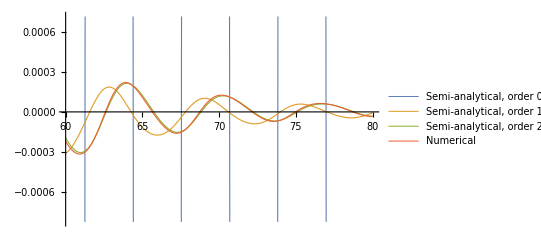

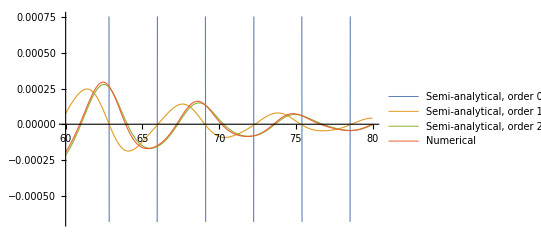

```mathematica
(*COMPARE NUMERICAL AND ANALYTICAL SOLUTION*)
nOrder plot=nmax;
listOfFunctions x = Flatten[{Table[completexSol[upToOrder]/.params //Chop,{upToOrder,0,nOrder plot}],numSol x[t]}];
listOfFunctions v = Flatten[{Table[completevSol[upToOrder]/.params //Chop,{upToOrder,0,nOrder plot}],numSol v[t]}];
listOfLabels = Flatten[{Table["Semi-analytical, order " <>ToString[upToOrder],{upToOrder,0,nOrder plot}],"Numerical"}];
Plot[listOfFunctions x,{t,60,80},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
Plot[listOfFunctions v,{t,60,80},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
```

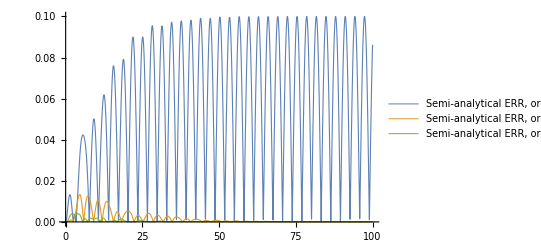

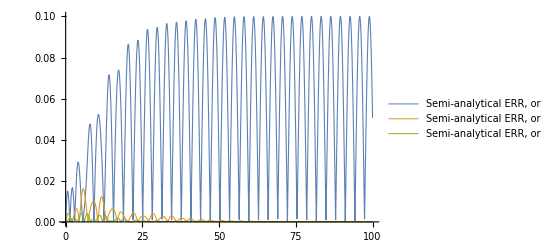

```mathematica
(*COMPARE ABSOLUTE ERRORS*)
nOrder plot=nmax;
listOfFunctions x = Flatten[Table[Abs[(completexSol[upToOrder]/.params //Chop)-numSol x[t]],{upToOrder,0,nOrder plot}]];
listOfFunctions v = Flatten[Table[Abs[(completevSol[upToOrder]/.params //Chop)-numSol v[t]],{upToOrder,0,nOrder plot}]];
listOfLabels = Flatten[Table["Semi-analytical ERR, order " <>ToString[upToOrder],{upToOrder,0,nOrder plot}]];
Plot[listOfFunctions x,{t,0,100},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
Plot[listOfFunctions v,{t,0,100},PlotLegends->listOfLabels,PlotStyle->Thickness[0.002]]
```